```mathematica
(*Ejercicio 1*)
AFD2AC[AFD_]:= Module[{i, j, k, ac, S, F, delta},
ac = {};
S = Union[AFD[[1]], AFD[[2]]];
F = AFD[[5]];
delta = AFD[[3]];
For[i = 1, i ≤ 2, i+=1,
For[j = 1, j ≤ Length[AFD[[i]]], j+=1,
For[k = 1, k ≤ Length[AFD[[i]]], k+=1,
	AppendTo[delta, {AFD[[i]][[j]],AFD[[i]][[k]],AFD[[i]][[k]]}];
];
];
];
ac = {S, delta, F};
Return[ac];
];

afd = {{q, p, r}, {a, b}, {{q, a, p}, {q, b, r}, {p, a, r}, {p, b, q}, {r, a, r}, {r, b, r}}, q, {r}}

ac = AFD2AC[afd]
```

{{q,p,r},{a,b},{{q,a,p},{q,b,r},{p,a,r},{p,b,q},{r,a,r},{r,b,r}},q,{r}}

{{a,b,p,q,r},{{q,a,p},{q,b,r},{p,a,r},{p,b,q},{r,a,r},{r,b,r},{q,q,q},{q,p,p},{q,r,r},{p,q,q},{p,p,p},{p,r,r},{r,q,q},{r,p,p},{r,r,r},{a,a,a},{a,b,b},{b,a,a},{b,b,b}},{r}}

```mathematica
(*Ejercicio 2*)
ACreconocedor[w_List, AC_, q_]:=Module[{cadena, i, destino,j},
cadena = w;
For[i = 1, i ≤ Length[cadena], i +=1,
(*Saco el nodo al que puedo llegar*)
destino = {Cases[AC[[2]],  {q, cadena[[1]], _}][[1,3]]};
For[j=2, j ≤ Length[cadena], j ++,
	destino = AppendTo[destino, Cases[AC[[2]], {cadena[[j - 1]], cadena[[j]], _}][[1,3]]];
];
cadena = destino;
];
If[MemberQ[AC[[3]],cadena[[Length[w]]]],
Return[True], 
Return[False]
];
];
AC = AFD2AC[afd]
ACreconocedor[{a,b,a,a,b}, AC, q]
```

{{a,b,p,q,r},{{q,a,p},{q,b,r},{p,a,r},{p,b,q},{r,a,r},{r,b,r},{q,q,q},{q,p,p},{q,r,r},{p,q,q},{p,p,p},{p,r,r},{r,q,q},{r,p,p},{r,r,r},{a,a,a},{a,b,b},{b,a,a},{b,b,b}},{r}}

True

```mathematica
(*Ejercicio 3*)
ACEquivalente[AFD_]:=Module[{AFDC, i, j ,aux},
AFDC = AFD2AC[AFD];
aux = {};
For[i=1, i≤Length[AFDC[[2]]],i+=1,
For[j = 1, j ≤ Length[AFDC[[1]]], j+=1,
aux = AppendTo[aux, {AFDC[[2, i, 1]], AFDC[[2, i, 2]], AFDC[[2,i ,2]],AFDC[[1,j]], AFDC[[2,i,3]]}];
];
];
AFDC[[2]] = aux;
Return[AFDC];
];
ACEquivalente[afd]
```

{{a,b,p,q,r},{{q,a,a,a,p},{q,a,a,b,p},{q,a,a,p,p},{q,a,a,q,p},{q,a,a,r,p},{q,b,b,a,r},{q,b,b,b,r},{q,b,b,p,r},{q,b,b,q,r},{q,b,b,r,r},{p,a,a,a,r},{p,a,a,b,r},{p,a,a,p,r},{p,a,a,q,r},{p,a,a,r,r},{p,b,b,a,q},{p,b,b,b,q},{p,b,b,p,q},{p,b,b,q,q},{p,b,b,r,q},{r,a,a,a,r},{r,a,a,b,r},{r,a,a,p,r},{r,a,a,q,r},{r,a,a,r,r},{r,b,b,a,r},{r,b,b,b,r},{r,b,b,p,r},{r,b,b,q,r},{r,b,b,r,r},{q,q,q,a,q},{q,q,q,b,q},{q,q,q,p,q},{q,q,q,q,q},{q,q,q,r,q},{q,p,p,a,p},{q,p,p,b,p},{q,p,p,p,p},{q,p,p,q,p},{q,p,p,r,p},{q,r,r,a,r},{q,r,r,b,r},{q,r,r,p,r},{q,r,r,q,r},{q,r,r,r,r},{p,q,q,a,q},{p,q,q,b,q},{p,q,q,p,q},{p,q,q,q,q},{p,q,q,r,q},{p,p,p,a,p},{p,p,p,b,p},{p,p,p,p,p},{p,p,p,q,p},{p,p,p,r,p},{p,r,r,a,r},{p,r,r,b,r},{p,r,r,p,r},{p,r,r,q,r},{p,r,r,r,r},{r,q,q,a,q},{r,q,q,b,q},{r,q,q,p,q},{r,q,q,q,q},{r,q,q,r,q},{r,p,p,a,p},{r,p,p,b,p},{r,p,p,p,p},{r,p,p,q,p},{r,p,p,r,p},{r,r,r,a,r},{r,r,r,b,r},{r,r,r,p,r},{r,r,r,q,r},{r,r,r,r,r},{a,a,a,a,a},{a,a,a,b,a},{a,a,a,p,a},{a,a,a,q,a},{a,a,a,r,a},{a,b,b,a,b},{a,b,b,b,b},{a,b,b,p,b},{a,b,b,q,b},{a,b,b,r,b},{b,a,a,a,a},{b,a,a,b,a},{b,a,a,p,a},{b,a,a,q,a},{b,a,a,r,a},{b,b,b,a,b},{b,b,b,b,b},{b,b,b,p,b},{b,b,b,q,b},{b,b,b,r,b}},{r}}

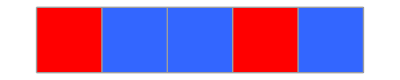
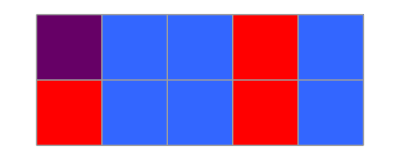
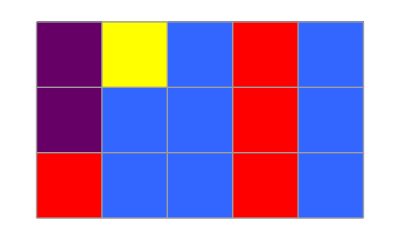
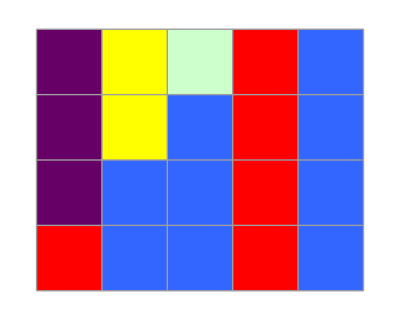
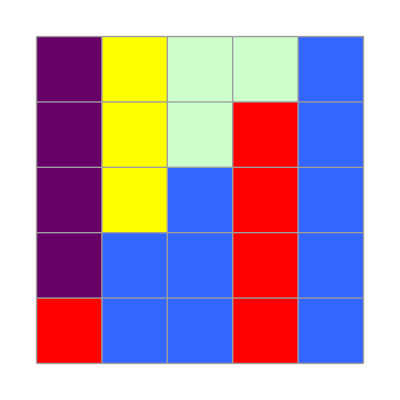
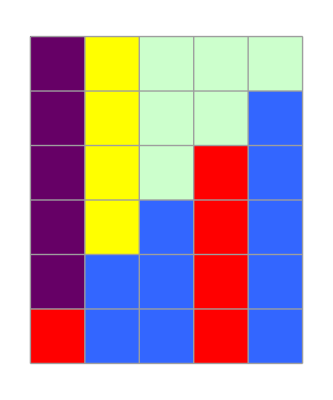
Soluciones {-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
(*Ejercicio 4*)
MuestraSecuencia[w_List, AC_, q_]:= Module[{i, j,secuencia,destino, aux, frames},
secuencia = {w};
frames = {ArrayPlot[{}]};
frames = AppendTo[frames, ArrayPlot[secuencia,ColorRules->{a->Red,b->RGBColor[0.2,0.4,1],q->Yellow,p->RGBColor[0.4,0,0.4],r->RGBColor[0.8,1,0.8]},Mesh->True]];
For[i = 1, i≤ Length[w], i+=1,
destino= {Cases[AC[[2]], {q, secuencia[[1,1]],_}][[1,3]]};
For[j=2, j ≤ Length[secuencia[[1]]],j +=1,
AppendTo[destino,Cases[AC[[2]],{secuencia[[1,j-1]],secuencia[[1,j]],_}][[1,3]]];
];

frames = AppendTo[frames,ArrayPlot[PrependTo[secuencia, destino],ColorRules->{a->Red,b->RGBColor[0.2,0.4,1],q->Yellow,p->RGBColor[0.4,0,0.4],r->RGBColor[0.8,1,0.8]},Mesh->True]
(*Muestro la solucion*)
]];
Print["Soluciones ", frames];
ListAnimate[frames]
];

w = {a,b,b,a,b};
MuestraSecuencia[w, AC, q]
```